```mathematica
Quit[]
```

This notebook can be used to find the thermal history of the Universe in the presence of a very light and weakly coupled neutrinophilic scalar. Relevant equations and details can be found in Escudero 2001.XXXXX.

### Basic Instructions

The code works as follows: 

1) Evaluate the Basic Modules Section. 
2) Evaluate the Neutrinophilic Scalar Section. It takes ~.1d20 s per example evaluation.

Note that everything is in MeV Units but the rates, the Hubble parameter and time which are in seconds

### Basic Modules (need to be loaded first)

This Section loads the main common Modules: 
	1) Thermodynamic Formulae 
	2) Finite Temperature QED corrections
	3) SM ν-ν and ν-e Interaction Rates
	4) Constants and Parameters
	
These modules are loaded from BasicModules.m. One can alternatively copy the content of BasicModules.nb here and load it locally.

```mathematica
(* Load Basic Modules *)
SetDirectory[NotebookDirectory[]];
Quiet[<<BasicModules.m];
```

### Light and Weakly Coupled Neutrinophilic Scalar ϕ

#### Hubble Parameter and total Energy and Pressure of the Universe

```mathematica
Clear[ρtot,ρtotMless,Hubble,HubbleMless,ptot,ptotMless,RHSec,RHSecMless];
(*Here we define two set of global thermodynamic quantities. Ones assuming mϕ = 0 while others allow for mϕ ≠ 0. *)
ρtot[Tγ_,Tν_,μν_,Tϕ_,μϕ_,mϕ_]:=(2ρBE[Tγ,0]+6ρFD[Tν,μν]+ρBEM[Tϕ,μϕ,mϕ]);
ρtotMless[Tγ_,Tν_,μν_,Tϕ_,μϕ_,mϕ_]:=(2ρBE[Tγ,0]+6ρFD[Tν,μν]+ρBE[Tϕ,μϕ]);

Hubble[Tγ_,Tν_,μν_,Tϕ_,μϕ_,mϕ_]:= (ρtot[Tγ,Tν,μν,Tϕ,μϕ,mϕ] (8 π)/(3 Mpl^2))^(1/2)FacMeVtos1;
HubbleMless[Tγ_,Tν_,μν_,Tϕ_,μϕ_,mϕ_]:= (ρtotMless[Tγ,Tν,μν,Tϕ,μϕ,mϕ] (8 π)/(3 Mpl^2))^(1/2)FacMeVtos1;

ptot[Tγ_,Tν_,μν_,Tϕ_,μϕ_,mϕ_]:=(1/3( 2ρBE[Tγ,0]+6ρFD[Tν,μν])+pBEM[Tϕ,μϕ,mϕ]);
ptotMless[Tγ_,Tν_,μν_,Tϕ_,μϕ_,mϕ_]:=(1/3( 2ρBE[Tγ,0]+6ρFD[Tν,μν])+pBE[Tϕ,μϕ]);

RHSec[Tγ_,Tν_,μν_,Tϕ_,μϕ_,mϕ_]:=-3 Hubble[Tγ,Tν,μν,Tϕ,μϕ,mϕ](ρtot[Tγ,Tν,μν,Tϕ,μϕ,mϕ]+ ptot[Tγ,Tν,μν,Tϕ,μϕ,mϕ]);

RHSecMless[Tγ_,Tν_,μν_,Tϕ_,μϕ_,mϕ_]:=-3 HubbleMless[Tγ,Tν,μν,Tϕ,μϕ,mϕ](ρtotMless[Tγ,Tν,μν,Tϕ,μϕ,mϕ]+ ptotMless[Tγ,Tν,μν,Tϕ,μϕ,mϕ]);
```

#### Energy and Number exchange rates in the MB approx

```mathematica
Clear[δnδtdecMB,δρδtdecMB];
(* Equations 2.10 and 2.11 of 2001.XXXXX. Also Equations 4.3a and 4.3b of 2001.XXXXX. *)
δnδtdecMB[λ_,ma_,Ta_,T_,μa_,μ_]:= FacMeVtos1*(3(ma λ^2)/(16 π))(ma^2(ⅇ^((2 μ)/T) T BesselK[1,ma/T]-ⅇ^(μa/Ta) Ta BesselK[1,ma/Ta]))/(2 π^2);

δρδtdecMB[λ_,ma_,Ta_,T_,μa_,μ_]:= FacMeVtos1*(3(ma λ^2)/(16 π))(ma^3(ⅇ^((2 μ)/T) T BesselK[2,ma/T]-ⅇ^(μa/Ta) Ta BesselK[2,ma/Ta]))/(2 π^2);
```

#### Temperature and Chemical Potential ODEs

```mathematica
Clear[dTνdt,dμνdt,dTϕdt,dμϕdt];

(* Equation 4.5c of 2001.XXXXX *)
dTνdt[Tγ_,Tν_,μν_,Tϕ_,μϕ_,mϕ_,λ_]:=1/(dnFDdμ[Tν,μν]dρFDdT[Tν,μν]-dnFDdT[Tν,μν]dρFDdμ[Tν,μν])(- 3 Hubble[Tγ,Tν,μν,Tϕ,μϕ,mϕ] ( (ρFD[Tν,μν]+pFD[Tν,μν])dnFDdμ[Tν,μν]-nFD[Tν,μν]dρFDdμ[Tν,μν]) +dnFDdμ[Tν,μν] 1/2(-1/3 δρδtdecMB[λ,mϕ,Tϕ,Tν,μϕ,μν])-dρFDdμ[Tν,μν] 1/2(-2/3 δnδtdecMB[λ,mϕ,Tϕ,Tν,μϕ,μν]));(*The factor of 1/2 accounts for the fact that we are considering a single neutrino species, not the neutrino + antineutrino *)

(* Equation 4.5d of 2001.XXXXX *)
dμνdt[Tγ_,Tν_,μν_,Tϕ_,μϕ_,mϕ_,λ_]:=-1/(dnFDdμ[Tν,μν]dρFDdT[Tν,μν]-dnFDdT[Tν,μν]dρFDdμ[Tν,μν])(- 3 Hubble[Tγ,Tν,μν,Tϕ,μϕ,mϕ] ((ρFD[Tν,μν]+pFD[Tν,μν])dnFDdT[Tν,μν]-nFD[Tν,μν]dρFDdT[Tν,μν]) +dnFDdT[Tν,μν] 1/2(-1/3 δρδtdecMB[λ,mϕ,Tϕ,Tν,μϕ,μν])-dρFDdT[Tν,μν] 1/2(-2/3 δnδtdecMB[λ,mϕ,Tϕ,Tν,μϕ,μν]));

(* Equation 4.5a of 2001.XXXXX *)
dTϕdt[Tγ_,Tν_,μν_,Tϕ_,μϕ_,mϕ_,λ_]:=1/(dndμBEM[Tϕ,μϕ,mϕ]dρdTBEM[Tϕ,μϕ,mϕ]-dndTBEM[Tϕ,μϕ,mϕ]dρdμBEM[Tϕ,μϕ,mϕ])(- 3 Hubble[Tγ,Tν,μν,Tϕ,μϕ,mϕ]( (ρBEM[Tϕ,μϕ,mϕ]+pBEM[Tϕ,μϕ,mϕ])dndμBEM[Tϕ,μϕ,mϕ]-nBEM[Tϕ,μϕ,mϕ]dρdμBEM[Tϕ,μϕ,mϕ]) +dndμBEM[Tϕ,μϕ,mϕ]δρδtdecMB[λ,mϕ,Tϕ,Tν,μϕ,μν]-dρdμBEM[Tϕ,μϕ,mϕ]δnδtdecMB[λ,mϕ,Tϕ,Tν,μϕ,μν]);

(* Equation 4.5b of 2001.XXXXX *)
dμϕdt[Tγ_,Tν_,μν_,Tϕ_,μϕ_,mϕ_,λ_]:=-1/(dndμBEM[Tϕ,μϕ,mϕ]dρdTBEM[Tϕ,μϕ,mϕ]-dndTBEM[Tϕ,μϕ,mϕ]dρdμBEM[Tϕ,μϕ,mϕ])(- 3 Hubble[Tγ,Tν,μν,Tϕ,μϕ,mϕ] ((ρBEM[Tϕ,μϕ,mϕ]+pBEM[Tϕ,μϕ,mϕ])dndTBEM[Tϕ,μϕ,mϕ]-nBEM[Tϕ,μϕ,mϕ]dρdTBEM[Tϕ,μϕ,mϕ]) +dndTBEM[Tϕ,μϕ,mϕ]δρδtdecMB[λ,mϕ,Tϕ,Tν,μϕ,μν]-dρdTBEM[Tϕ,μϕ,mϕ]δnδtdecMB[λ,mϕ,Tϕ,Tν,μϕ,μν]);
```

#### Temperature and Chemical Potential ODEs mϕ = 0

```mathematica
Clear[dTνdtMless,dμνdtMless,dTϕdtMless,dμϕdtMless];
(* Same as the previous subsection but particularizing the Thermodynamics for mϕ=0 *)
dTνdtMless[Tγ_,Tν_,μν_,Tϕ_,μϕ_,mϕ_,λ_]:=1/(dnFDdμ[Tν,μν]dρFDdT[Tν,μν]-dnFDdT[Tν,μν]dρFDdμ[Tν,μν])(- 3 HubbleMless[Tγ,Tν,μν,Tϕ,μϕ,mϕ] ( (ρFD[Tν,μν]+pFD[Tν,μν])dnFDdμ[Tν,μν]-nFD[Tν,μν]dρFDdμ[Tν,μν]) +dnFDdμ[Tν,μν] 1/2(-1/3 δρδtdecMB[λ,mϕ,Tϕ,Tν,μϕ,μν])-dρFDdμ[Tν,μν] 1/2(-2/3 δnδtdecMB[λ,mϕ,Tϕ,Tν,μϕ,μν]));(*The factor of 1/2 accounts for the fact that we are considering a single neutrino species, not the neutrino + antineutrino *)

dμνdtMless[Tγ_,Tν_,μν_,Tϕ_,μϕ_,mϕ_,λ_]:=-1/(dnFDdμ[Tν,μν]dρFDdT[Tν,μν]-dnFDdT[Tν,μν]dρFDdμ[Tν,μν])(- 3 HubbleMless[Tγ,Tν,μν,Tϕ,μϕ,mϕ] ((ρFD[Tν,μν]+pFD[Tν,μν])dnFDdT[Tν,μν]-nFD[Tν,μν]dρFDdT[Tν,μν]) +dnFDdT[Tν,μν] 1/2(-1/3 δρδtdecMB[λ,mϕ,Tϕ,Tν,μϕ,μν])-dρFDdT[Tν,μν] 1/2(-2/3 δnδtdecMB[λ,mϕ,Tϕ,Tν,μϕ,μν]));

dTϕdtMless[Tγ_,Tν_,μν_,Tϕ_,μϕ_,mϕ_,λ_]:=1/(dnBEdμ[Tϕ,μϕ]dρBEdT[Tϕ,μϕ]-dnBEdT[Tϕ,μϕ]dρBEdμ[Tϕ,μϕ])(- 3 HubbleMless[Tγ,Tν,μν,Tϕ,μϕ,mϕ]( (ρBE[Tϕ,μϕ]+pBE[Tϕ,μϕ])dnBEdμ[Tϕ,μϕ]-nBE[Tϕ,μϕ]dρBEdμ[Tϕ,μϕ]) +dnBEdμ[Tϕ,μϕ]δρδtdecMB[λ,mϕ,Tϕ,Tν,μϕ,μν]-dρBEdμ[Tϕ,μϕ]δnδtdecMB[λ,mϕ,Tϕ,Tν,μϕ,μν]);

dμϕdtMless[Tγ_,Tν_,μν_,Tϕ_,μϕ_,mϕ_,λ_]:=-1/(dnBEdμ[Tϕ,μϕ]dρBEdT[Tϕ,μϕ]-dnBEdT[Tϕ,μϕ]dρBEdμ[Tϕ,μϕ])(- 3 HubbleMless[Tγ,Tν,μν,Tϕ,μϕ,mϕ] ((ρBE[Tϕ,μϕ]+pBE[Tϕ,μϕ])dnBEdT[Tϕ,μϕ]-nBE[Tϕ,μϕ]dρBEdT[Tϕ,μϕ]) +dnBEdT[Tϕ,μϕ]δρδtdecMB[λ,mϕ,Tϕ,Tν,μϕ,μν]-dρBEdT[Tϕ,μϕ]δnδtdecMB[λ,mϕ,Tϕ,Tν,μϕ,μν]);
```

#### Definition of observables

```mathematica
Clear[Nefffunc,gstars,gstar,OmeganuMdiv];

Nefffunc[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=8/7(11/4)^(4/3)(2 ρFD[Tνe,μνe]+4 ρFD[Tνμ,μνμ])/(2ρBE[Tγ,0]);

gstars[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=45/(2 π^2 Tγ^3)(2 sFD[Tνe,μνe]+4sFD[Tνμ,μνμ]+2sBE[Tγ,0]+4sFDM[Tγ,0,me]);


gstar[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=30/π^2(2 ρFD[Tνe,μνe]+4 ρFD[Tνμ,μνμ]+2ρBE[Tγ,0])/Tγ^4;

OmeganuMdiv[Tγ_,Tνe_,Tνμ_,μνe_,μνμ_]:=(3/2 rhocrit/Tγ00^3 Tγ^3/(nFD[Tνe,μνe]+2nFD[Tνμ,μνμ]))/.{rhocrit-> 8.0992 10^-11 eV^4,Tγ00-> 2.7255 Kel}/.{Kel-> 1/(1.16045 10^4)eV}/.eV-> 1;
```

#### Key Functions

Here we comment on the description of each of the main functions together with some useful comments. 

1) FuncϕMless[Γeff_,mϕ_,Tminrat_]: 
Computes the themodynamic evolution assuming mϕ = 0 up to a neutrino temperature of Tminrat * mϕ. 
The integration starts at Tν0=100mϕ; So, a reasonable Tminrat to use is Tminrat = 20.
Outputs the final time and relevant thermodynamic quantities: tmax,Tγ0,Tν0,μν0,Tϕ0,μϕ0.

2) FuncϕThermo[Γeff_,mϕ_]:
Computes the themodynamic evolution starting from the result of FuncϕMless[λ,mϕ,20]. 
It has been tested to work well for 10^-5<Γeff < 10^3.
Runs from the starting time given by FuncϕMless and stops at a time such that Tν ~ mϕ/18 or t = 5 × τϕ. So that the ϕ population is negligible then.
Outputs Tγ[t],Tν[t],μν[t],Tϕ[t],μϕ[t], t0, tmax

3) FuncϕPlots[Γeff_,mϕ_]:
Calls FuncϕThermo[Γeff,mϕ] and prints and outputs Neff, the relevant thermodynamic quantities and plots of the energy density of the relevant species,  and of the evolution of the thermodynamic quantities. 

4) FuncϕOutput[Γeff_,mϕ_,filename_] : 
The function calls FuncϕThermo[Γeff,mϕ] and outputs to the file “nuScalar/filename.dat” the relevant thermodynamic evolution
Outputs a table containing:
t, Tγ/mϕ, Tν/Tγ, μν/Tγ, TZ/Tγ, μZ/Tγ, Hub/Tγ^2, ρtot/Tγ^4, ptot/Tγ^4, ρν/Tγ^4,ρZ/Tγ^4,pZ/Tγ^4, nν/Tγ^3,nZ/Tγ^3

5) FuncϕSimple[Γeff_,mϕ_] : 
Simply returns the asymptotic value of N_eff,  g_(*s) ,  g_*,   ∑m_ν/Ω_ν,   T_γ/T_ν,   T_ν/μ_ν

```mathematica
FuncϕMless[Γeff_,mϕ_,Tminrat_]:=(
λeff=4 10^-12 √Γeff √(mϕ/10^-3);(* Equation 4.4 of 2001.XXXXX *)

(* Initial conditions as in Equation 4.6 of 2001.XXXXX *)
Tν0=100mϕ;
Tγ0=1.39583 Tν0;
μν0=-Tν0 10^-4;
Tϕ0=10^-3 Tν0;
μϕ0=-10^-5 Tν0;

(*Tν0=100mϕ;
Tγ0=1.39440 Tν0;
μν0=-Tν0/239.4;
Tϕ0=10^-3 Tν0;
μϕ0=-10^-4Tν0;
*)
t0=1/(2 HubbleMless[Tγ0,Tν0,μν0,Tϕ0,μϕ0,mϕ]);
tmax=1/(2 HubbleMless[1.4 Tminrat mϕ,Tminrat mϕ,0,10^-3 Tminrat mϕ,0,mϕ]);
solEarlyUniverse=NDSolve[{
Tγ'[t]==-HubbleMless[Tγ[t],Tν[t],μν[t],Tϕ[t],μϕ[t],mϕ]Tγ[t],
Tν'[t]==dTνdtMless[Tγ[t],Tν[t],μν[t],Tϕ[t],μϕ[t],mϕ,λeff],
μν'[t]==dμνdtMless[Tγ[t],Tν[t],μν[t],Tϕ[t],μϕ[t],mϕ,λeff],
Tϕ'[t]==dTϕdtMless[Tγ[t],Tν[t],μν[t],Tϕ[t],μϕ[t],mϕ,λeff],
μϕ'[t]==dμϕdtMless[Tγ[t],Tν[t],μν[t],Tϕ[t],μϕ[t],mϕ,λeff],
Tγ[t0]==Tγ0,Tν[t0]==Tν0,μν[t0]==μν0,Tϕ[t0]==Tϕ0,μϕ[t0]==μϕ0},{Tγ,Tν,μν,Tϕ,μϕ},{t,t0,tmax},AccuracyGoal->14,PrecisionGoal->14];

Tγ0=(Tγ[t]/.solEarlyUniverse/.{t-> tmax})[[1]]//N;
Tν0=(Tν[t]/.solEarlyUniverse/.{t-> tmax})[[1]]//N;
μν0=(μν[t]/.solEarlyUniverse/.{t-> tmax})[[1]]//N;
Tϕ0=(Tϕ[t]/.solEarlyUniverse/.{t-> tmax})[[1]]//N;
μϕ0=(μϕ[t]/.solEarlyUniverse/.{t-> tmax})[[1]]//N;

{tmax,Tγ0,Tν0,μν0,Tϕ0,μϕ0});

FuncϕThermo[Γeff_,mϕ_]:=(

tCPU1=TimeUsed[];
λeff=4 10^-12 √Γeff √(mϕ/10^-3);(* Equation 4.4 of 2001.XXXXX *)
SetDirectory[NotebookDirectory[]];
resvec=Quiet[FuncϕMless[Γeff,mϕ,20]];
t0=resvec[[1]];Tγ0=resvec[[2]];Tν0=resvec[[3]];μν0=resvec[[4]];Tϕ0=resvec[[5]];μϕ0=resvec[[6]];


Tmin=mϕ/18;
tmax=Max[1/(2 HubbleMless[1.40201 Tmin,Tmin,0,10^-4 Tmin,0,10^-5 Tmin]),12 (3(λeff^2 mϕ)/(16 π))^-1/FacMeVtos1];


solEarlyUniverse=NDSolve[{
Tγ'[t]==-Hubble[Tγ[t],Tν[t],μν[t],Tϕ[t],μϕ[t],mϕ]Tγ[t],
Tν'[t]==dTνdt[Tγ[t],Tν[t],μν[t],Tϕ[t],μϕ[t],mϕ,λeff],
μν'[t]==dμνdt[Tγ[t],Tν[t],μν[t],Tϕ[t],μϕ[t],mϕ,λeff],
Tϕ'[t]==dTϕdt[Tγ[t],Tν[t],μν[t],Tϕ[t],μϕ[t],mϕ,λeff],
μϕ'[t]==dμϕdt[Tγ[t],Tν[t],μν[t],Tϕ[t],μϕ[t],mϕ,λeff],
Tγ[t0]==Tγ0,Tν[t0]==Tν0,μν[t0]==μν0,Tϕ[t0]==Tϕ0,μϕ[t0]==μϕ0},{Tγ,Tν,μν,Tϕ,μϕ},{t,t0,tmax},PrecisionGoal->10,AccuracyGoal->10,Method->{"EquationSimplification"->"Residual"}];


tCPU2=TimeUsed[];
Print["tCPU = ", tCPU2-tCPU1];

Tγoftfunc[t1_]:=(Tγ[t]/.solEarlyUniverse)[[1]]/.{t-> t1};
Tνoftfunc[t1_]:=(Tν[t]/.solEarlyUniverse)[[1]]/.{t-> t1};
μνoftfunc[t1_]:=(μν[t]/.solEarlyUniverse)[[1]]/.{t-> t1};
Tϕoftfunc[t1_]:=(Tϕ[t]/.solEarlyUniverse)[[1]]/.{t-> t1};
μϕoftfunc[t1_]:=(μϕ[t]/.solEarlyUniverse)[[1]]/.{t-> t1};

{Tγoftfunc[t],Tνoftfunc[t],μνoftfunc[t],Tϕoftfunc[t],μϕoftfunc[t],t0,tmax,tCPU2-tCPU1});
FuncϕPlots[Γeff_,mϕ_]:=(

resvecaux=Quiet[FuncϕThermo[Γeff,mϕ]];(* Obtain the relevant Thermodynamic evolution *)

Clear[Tγoft,Tνoft,μνoft,Tϕoft,μϕoft,tofTγ];
Tγoft[tt_]:=resvecaux[[1]]/.{t-> tt};
Tνoft[tt_]:=resvecaux[[2]]/.{t-> tt};
μνoft[tt_]:=resvecaux[[3]]/.{t-> tt};
Tϕoft[tt_]:=resvecaux[[4]]/.{t-> tt};
μϕoft[tt_]:=resvecaux[[5]]/.{t-> tt};
t0=resvecaux[[6]];
tmax=resvecaux[[7]];
tCPUtot=resvecaux[[8]];
tofTγ[Tgam_]:= InverseFunction[Tγoft][Tgam];

Neffval=Nefffunc[Tγoft[tmax],Tνoft[tmax],Tνoft[tmax],μνoft[tmax],μνoft[tmax]];
gstarval=gstar[Tγoft[tmax],Tνoft[tmax],Tνoft[tmax],μνoft[tmax],μνoft[tmax]];
gstarsval=gstars[Tγoft[tmax],Tνoft[tmax],Tνoft[tmax],μνoft[tmax],μνoft[tmax]];
omeganuval=OmeganuMdiv[Tγoft[tmax],Tνoft[tmax],Tνoft[tmax],μνoft[tmax],μνoft[tmax]];
Tratio=Tγoft[tmax]/Tνoft[tmax];
μratio=Tνoft[tmax]/μνoft[tmax];


Print["N_eff     = ", SetPrecision[Neffval,6]];
Print["g_(*s)      = ", SetPrecision[gstarsval,4]];
Print["g_*      = ", SetPrecision[gstarval,4]];
Print["∑m_ν/Ω_ν  = ",SetPrecision[omeganuval,4] , " eV"];
Print["T_γ/T_ν   = ", SetPrecision[Tratio,6]];
Print["T_ν/μ_ν   = ", SetPrecision[μratio,6]];

plotρ=LogLogPlot[{0.0411,Quiet[ρBEM[Tϕoft[tofTγ[Tνeff 1.402 mϕ]],μϕoft[tofTγ[Tνeff 1.402 mϕ]],mϕ]]/Tγoft[tofTγ[Tνeff 1.402 mϕ]]^4,ρFD[Tνoft[tofTγ[Tνeff 1.402 mϕ]],μνoft[tofTγ[Tνeff 1.402 mϕ]]]/Tγoft[tofTγ[Tνeff 1.402 mϕ]]^4},{ Tνeff,10,1/15},PlotStyle->{{Green,Dotted},{Dashed,Red},Blue,{Dashed,Black}},PlotLegends->{"ρϕ/Tγ^4|max","ρϕ/Tγ^4","ρν/Tγ^4"},AxesLabel->{"Tνeff/mϕ"}];

plotρt=LogLogPlot[{0.0411,Quiet[ρBEM[Tϕoft[t],μϕoft[t],mϕ]]/Tγoft[t]^4,ρFD[Tνoft[t],μνoft[t]]/Tγoft[t]^4},{ t,t0,tmax},PlotStyle->{{Green,Dotted},{Dashed,Red},Blue,{Dashed,Black}},PlotLegends->{"ρϕ/Tγ^4|max","ρϕ/Tγ^4","ρν/Tγ^4"},AxesLabel->{"t(s)"}];

plotchem=LogLogPlot[{Abs[μϕoft[t]/Tγoft[t]],Abs[(2μνoft[t])/Tγoft[t]],Abs[Tνoft[t]/Tγoft[t]],Abs[Tϕoft[t]/Tγoft[t]]},{ t,t0,tmax},PlotStyle->{{Red},{Green,Dotted},Blue,{Dashed,Black}},PlotLegends->{"|μϕ/Tγ|","|(2 μν)/Tγ|","|Tν/Tγ|","|Tϕ/Tγ|"},AxesLabel->{"t (s)"}];


ρtott[t_]:=Quiet[ρtot[Tγoft[t],Tνoft[t],μνoft[t],Tϕoft[t],μϕoft[t],mϕ]];
RHStott[t_]:=RHSec[Tγoft[t],Tνoft[t],μνoft[t],Tϕoft[t],μϕoft[t],mϕ];

tvec=Table[10^i,{i,Log10[t0],Log10[tmax],(Log10[tmax]-Log10[t0])*0.01}];
resvec=Table[Abs[1-RHStott[10^i]/ρtott'[10^i]],{i,Log10[t0],Log10[tmax],(Log10[tmax]-Log10[t0])*0.01}];

Totvec=Table[0,{i,1,Length[tvec]},{j,1,2}];
Totvec[[All,2]]=resvec;
Totvec[[All,1]]=Table[Tγoft[10^i]/mϕ,{i,Log10[t0],Log10[tmax],(Log10[tmax]-Log10[t0])*0.01}];

Plotenergycons=ListLogLogPlot[Totvec,PlotLegends->{"Abs[1+(3  H (ρ + P))/ρdot]"},AxesLabel->{"Tgam/mϕ"}];

Clear[Tγoft,Tνoft,μνoft,Tϕoft,μϕoft,tofTγ];

{plotρt,plotchem,Plotenergycons,plotρ,Neffval,SetPrecision[gstarsval,4],SetPrecision[gstarval,4],SetPrecision[omeganuval,4],SetPrecision[Tratio,6],SetPrecision[μratio,6],SetPrecision[tCPUtot,2]});


FuncϕSimple[Γeff_,mϕ_]:=(

resvecaux=Quiet[FuncϕThermo[Γeff,mϕ]];(* Obtain the relevant Thermodynamic evolution *)

Clear[Tγoft,Tνoft,μνoft,Tϕoft,μϕoft,tofTγ];
Tγoft[tt_]:=resvecaux[[1]]/.{t-> tt};
Tνoft[tt_]:=resvecaux[[2]]/.{t-> tt};
μνoft[tt_]:=resvecaux[[3]]/.{t-> tt};
Tϕoft[tt_]:=resvecaux[[4]]/.{t-> tt};
μϕoft[tt_]:=resvecaux[[5]]/.{t-> tt};
t0=resvecaux[[6]];
tmax=resvecaux[[7]];
tCPUtot=resvecaux[[8]];
tofTγ[Tgam_]:= InverseFunction[Tγoft][Tgam];

Neffval=Nefffunc[Tγoft[tmax],Tνoft[tmax],Tνoft[tmax],μνoft[tmax],μνoft[tmax]];
gstarval=gstar[Tγoft[tmax],Tνoft[tmax],Tνoft[tmax],μνoft[tmax],μνoft[tmax]];
gstarsval=gstars[Tγoft[tmax],Tνoft[tmax],Tνoft[tmax],μνoft[tmax],μνoft[tmax]];
omeganuval=OmeganuMdiv[Tγoft[tmax],Tνoft[tmax],Tνoft[tmax],μνoft[tmax],μνoft[tmax]];
Tratio=Tγoft[tmax]/Tνoft[tmax];
μratio=Tνoft[tmax]/μνoft[tmax];

{SetPrecision[Neffval,6],SetPrecision[gstarsval,4],SetPrecision[gstarval,4],SetPrecision[omeganuval,4],SetPrecision[Tratio,6],SetPrecision[μratio,6],SetPrecision[tCPUtot,2]});


FuncϕOutput[Γeff_,mϕ_,filename_]:=(

resvecaux=Quiet[FuncϕThermo[Γeff,mϕ]];(* Obtain the relevant Thermodynamic evolution *)

Clear[Tγoft,Tνoft,μνoft,Tϕoft,μϕoft,tofTγ,ρtotoft,ptotoft,Hubbleoft];
Tγoft[tt_]:=resvecaux[[1]]/.{t-> tt};
Tνoft[tt_]:=resvecaux[[2]]/.{t-> tt};
μνoft[tt_]:=resvecaux[[3]]/.{t-> tt};
Tϕoft[tt_]:=resvecaux[[4]]/.{t-> tt};
μϕoft[tt_]:=resvecaux[[5]]/.{t-> tt};
t0=resvecaux[[6]];
tmax=resvecaux[[7]];
tofTγ[Tgam_]:= InverseFunction[Tγoft][Tgam];


ρtotoft[t_]:=Quiet[ρtot[Tγoft[t],Tνoft[t],μνoft[t],Tϕoft[t],μϕoft[t],mϕ]];
ptotoft[t_]:=Quiet[ptot[Tγoft[t],Tνoft[t],μνoft[t],Tϕoft[t],μϕoft[t],mϕ]];
Hubbleoft[t_]:=Quiet[Hubble[Tγoft[t],Tνoft[t],μνoft[t],Tϕoft[t],μϕoft[t],mϕ]];

tvec=Table[10^i,{i,Log10[t0],Log10[tmax],(Log10[tmax]-Log10[t0])/400}];

Totvec=Table[0,{i,1,Length[tvec]},{j,1,14}];
For[i=1,i≤Length[tvec],i++,
time=tvec[[i]];
Tγtime=Tγoft[time];
Totvec[[i,1]]=time;
Totvec[[i,2]]=Tγoft[time]/mϕ;
Totvec[[i,3]]=Tνoft[time]/Tγtime;
Totvec[[i,4]]=μνoft[time]/Tγtime;
Totvec[[i,5]]=Tϕoft[time]/Tγtime;
Totvec[[i,6]]=μϕoft[time]/Tγtime;

Totvec[[i,7]]=Mpl/FacMeVtos1 Hubbleoft[time]/Tγtime^2;
Totvec[[i,8]]=ρtotoft[time]/Tγtime^4;
Totvec[[i,9]]=ptotoft[time]/Tγtime^4;

Totvec[[i,10]]=6ρFD[Tνoft[time],μνoft[time]]/Tγtime^4;
Totvec[[i,11]]=ρBEM[Tϕoft[time],μϕoft[time],mϕ]/Tγtime^4;
Totvec[[i,12]]=pBEM[Tϕoft[time],μϕoft[time],mϕ]/Tγtime^4;
Totvec[[i,13]]=6 nFD[Tνoft[time],μνoft[time]]/Tγtime^3;
Totvec[[i,14]]=nBEM[Tϕoft[time],μϕoft[time],mϕ]/Tγtime^3;

 ];
(* The table contains the following quantities: 
t, Tγ/mϕ, Tν/Tγ, μν/Tγ, TZ/Tγ, μZ/Tγ, Hub/Tγ^2, ρtot/Tγ^4, ptot/Tγ^4, ρν/Tγ^4,ρZ/Tγ^4,pZ/Tγ^4, nν/Tγ^3,nZ/Tγ^3*)

Totvec[[All,All]]=SetPrecision[Totvec[[All,All]],7];
Print["Thermodynamics are output to: Results/NuScalar/"<> filename<>".dat"];
Export["Results/NuScalar/"<> filename<>".dat",Totvec,"Table","FieldSeparators"->"      ","TableHeadings"-> {"#time (s)" ,"Tγ/mϕ   ",        "Tν/Tγ     ",           "μν/Tγ       ",            "Tϕ/Tγ    ",          "μϕ/Tγ   ",         "H/Tγ2  ",         "rhotot/Tγ4",    "ptot/Tγ4",       "ρnu/Tγ4  ",            "ρϕ/Tγ4      ",                "pϕ/Tγ4      ",               "nnu/Tγ3  ",             "nϕ/Tγ3"}];

Clear[Tγoft,Tνoft,μνoft,Tϕoft,μϕoft,tofTγ,ρtotoft,ptotoft,Hubbleoft,Totvec];

);
```

#### Some Examples

tCPU = 54.0534

N_eff     = 3.1623

g_(*s)      = 3.985

g_*      = 3.436

∑m_ν/Ω_ν  = 93.07 eV

T_γ/T_ν   = 1.33667

T_ν/μ_ν   = -7.05022

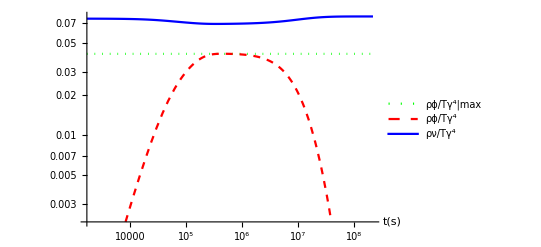

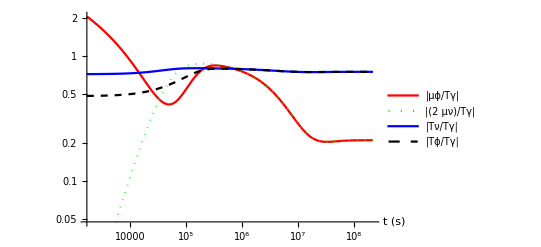

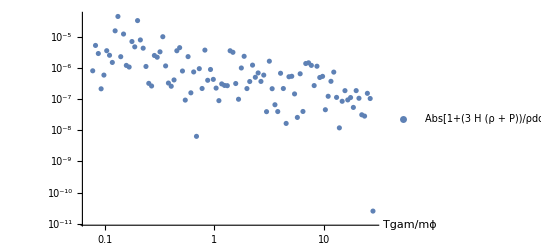

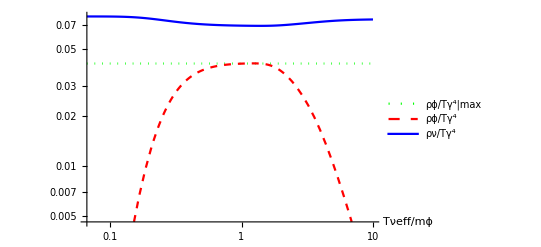

```mathematica
Γeffval=100;
mϕval=0.001;(* 1 keV *)
resvec=Quiet[FuncϕPlots[Γeffval,mϕval]];
resvec[[1]]
resvec[[2]]
resvec[[3]]
resvec[[4]]
```

tCPU = 54.78

N_eff     = 3.09392

g_(*s)      = 3.954

g_*      = 3.405

∑m_ν/Ω_ν  = 93.07 eV

T_γ/T_ν   = 1.37034

T_ν/μ_ν   = -16.5081

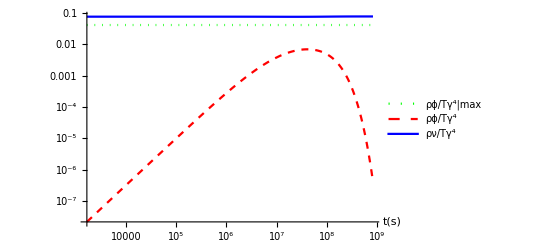

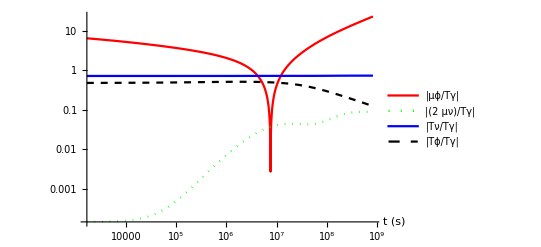

```mathematica
Γeffval=0.01;
mϕval=0.001;(* 1 keV *)
resvec=Quiet[FuncϕPlots[Γeffval,mϕval]];
resvec[[1]]
resvec[[2]]
```

tCPU = 63.6687

N_eff     = 3.16277

g_(*s)      = 3.985

g_*      = 3.437

∑m_ν/Ω_ν  = 93.07 eV

T_γ/T_ν   = 1.33642

T_ν/μ_ν   = -7.01963

Note the remarkable agreement with Expressions 4.12 and 4.13 of 2001.XXXXX

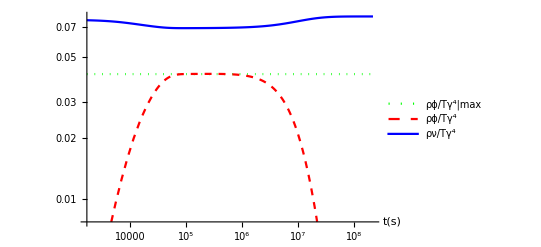

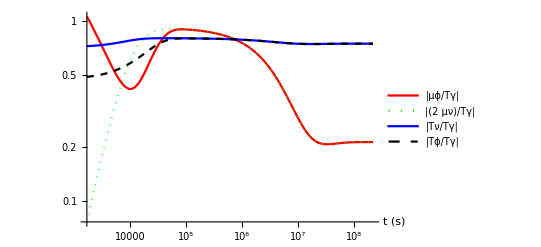

```mathematica
Γeffval=1000;
mϕval=0.001;(* 1 keV *)
resvec=Quiet[FuncϕPlots[Γeffval,mϕval]];
Print["Note the remarkable agreement with Expressions 4.12 and 4.13 of 2001.XXXXX "];
resvec[[1]]
resvec[[2]]
```

#### Output a file with the Thermodynamics

```mathematica
mϕp=0.001;(* Namely, 1 keV *)
Quiet[FuncϕOutput[100,mϕp,"Thermofast_100_keV"]]
```

tCPU = 50.6779

Thermodynamics are output to: Results/NuScalar/Thermofast_100_keV.dat